```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;rep={a1->Subscript[a, 1],a2->Subscript[a, 2],a3->Subscript[a, 3],κi->Subscript[κ, i],κr->Subscript[κ, r],kx->Subscript[k, x], ky->Subscript[k, y], kz->Subscript[k, z], vz->Subscript[v, z], vp->Subscript[v, p],en->e,b1->Subscript[b, 1],b2->Subscript[b, 2],b3->Subscript[b, 3]};
ass=Assumptions->{a1,b1,vz,v,ky,kz,κi,κr,t,μ}∈ Reals &&  k>0  && v>0 && μ>0;
Clear[ham,eval,dx,dy,dz,κ,k0];k0=1;
sx=({{0, 1}, {1, 0}});sy=({{0, -ⅈ}, {ⅈ, 0}});sz=({{1, 0}, {0, -1}});
id=({{1, 0}, {0, 1}});{dx,dy,dz}={ (kx^2-ky^2)/k0^2,(2 kx ky)/k0^2,kz};
ham=dx sx+dy sy+dz sz;
```

```mathematica
(* -Graphics- -Graphics-*)
(kx+ⅈ ky)^2(σx-ⅈ σy)/2+(kx-ⅈ ky)^2(σx+ⅈ σy)/2//FullSimplify
(kx+ⅈ ky)^3(σx-ⅈ σy)/2+(kx-ⅈ ky)^3(σx+ⅈ σy)/2//FullSimplify
```

kx^2 σx-ky^2 σx+2 kx ky σy

kx^3 σx-3 kx ky^2 σx+3 kx^2 ky σy-ky^3 σy

```mathematica
(*-Graphics-,-Graphics-*)
```

## analytics

```mathematica
ham/.{kx->-ⅈ Dx}//FullSimplify
Eigenvalues[ham]//FullSimplify
```

{{kz,-(Dx+ky)^2},{-(Dx-ky)^2,-kz}}

{-√((kx^2+ky^2)^2+kz^2),√((kx^2+ky^2)^2+kz^2)}

### Analytics

```mathematica
Clear[eq0,prod,solu,κ,κr,κi,a1,b1];
κ=κr+ⅈ κi;
ψ={1,a1+ⅈ b1};
ψdag={1,a1-ⅈ b1};
prod=FullSimplify[κi  ψdag.(sx.ψ)-ky ψdag.(sy.ψ),ass]/2;
eq0=Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1];
(* -((Dx^2+ky^2) sxψ)-2 ⅈ Dx ky syψ+kz szψ *)
eq=FullSimplify[(- ky^2 sx.ψ-κ^2 sx.ψ+2 ⅈ  ky κ sy.ψ+ kz sz.ψ - en id.ψ)]//FullSimplify;
κi=ky b1/a1;
eqn=(Flatten[FullSimplify[ComplexExpand[ReIm[ eq]],ass],1]//Expand)/.{ky^2->kysq,ky κr->kykr, κr^2->κrsq}
	solu[ky_,kz_]=FullSimplify[Solve[ (*-b1 ky+a1 κi==0&&*) eqn[[1]]==0  && eqn[[2]]==0 && eqn[[3]]==0  && eqn[[4]]==0 && κr≠0,{en,κr,κrsq,kykr,a1,b1}],ass]/.{kykr->ky κr,kysq->ky^2}
Clear[κ,κi,κr,en,a1];
```

{-en+2 a1 kykr+(2 b1^2 kykr)/a1-a1 kysq-(b1^2 kysq)/a1+kz-a1 κrsq,b1 kysq+(b1^3 kysq)/a1^2-b1 κrsq,-a1 en-2 kykr-kysq+(b1^2 kysq)/a1^2-a1 kz-κrsq,-b1 en-(2 b1 kykr)/a1-(2 b1 kysq)/a1-b1 kz}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{en→(kz+a1^2 kz+4 a1 ky κr)/(1-a1^2),κrsq→(ky^2-a1^2 ky^2+2 a1 kz+2 (1+a1^2) ky κr)/(-1+a1^2),b1→0},{en→-(4 (a1^2+b1^2) ky^2+a1 (-1+a1^2+b1^2) kz)/(a1 (1+a1^2+b1^2)),κrsq→ky^2+(b1^2 ky^2)/a1^2,ky κr→((-1+a1^2+b1^2) ky^2-a1 kz)/(1+a1^2+b1^2)},{κrsq→en-ky^2,ky κr→kz/2,a1→-1,b1→0},{κrsq→-en-ky^2,ky κr→-kz/2,a1→1,b1→0},{en→(kz κr)/ky,κrsq→-kz^2/(4 ky^2),a1→-(2 ky^2)/kz,b1→-(√(-4 ky^4-kz^2))/kz},{en→(kz κr)/ky,κrsq→-kz^2/(4 ky^2),a1→-(2 ky^2)/kz,b1→(√(-4 ky^4-kz^2))/kz}}

### sol 3: not admissible

```mathematica
ky^2+κr^2/.κr->kz/(2ky)
```

ky^2+kz^2/(4 ky^2)

```mathematica
{ener,kap}={ky^2+kz^2/(4 ky^2), kz/(2ky)};
soll=FullSimplify[Solve[kap==0 &&  ener==μ,{ky,kz}],ass]
FullSimplify[ √((ky^2)^2+kz^2)/.soll,ass]
```

{{ky→-√μ,kz→0},{ky→√μ,kz→0}}

{√(μ^2),√(μ^2)}

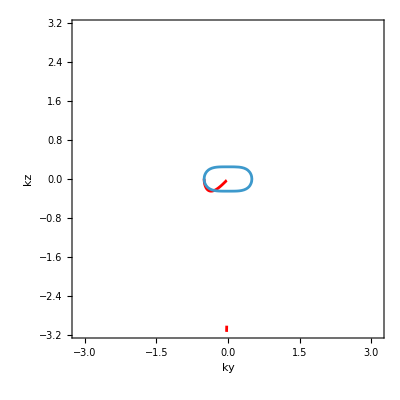

```mathematica
mu=0.25;lim=π;a1=0;Clear[κr];
c1=ContourPlot[ky^2+kz^2/(4 ky^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->Red, PlotLegends->Automatic,RegionFunction->Function[{ky,kz,z},((1+a1^2) ky)/(-1+a1^2)+√2 √((a1 (2 a1 ky^2+(-1+a1^2) kz))/((-1+a1^2)^2))>0 && kz/(2ky)>=0]]//Quiet;

fs=ContourPlot[√((ky^2)^2+(kz)^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},Contours->20,PlotLegends->Automatic];
Show[c1,fs]
Clear[κr,a1];
```

### sol 1 (not admissible)

```mathematica
Clear[a1];
vals=FullSimplify[Solve[κr^2==(ky^2-a1^2 ky^2+2 a1 kz+2 (1+a1^2) ky κr)/(-1+a1^2),κr],ass]
FullSimplify[(kz+a1^2 kz+4 a1 ky κr)/(1-a1^2)/.vals,ass]
```

{{κr→((1+a1^2) ky)/(-1+a1^2)-√2 √((a1 (2 a1 ky^2+(-1+a1^2) kz))/((-1+a1^2)^2))},{κr→((1+a1^2) ky)/(-1+a1^2)+√2 √((a1 (2 a1 ky^2+(-1+a1^2) kz))/((-1+a1^2)^2))}}

{(-4 a1 (1+a1^2) ky^2+kz-a1^4 kz+4 √2 a1 (-1+a1^2) ky √((a1 (2 a1 ky^2+(-1+a1^2) kz))/((-1+a1^2)^2)))/((-1+a1^2)^2),(kz+a1^2 kz+4 a1 ky (((1+a1^2) ky)/(-1+a1^2)+√2 √((a1 (2 a1 ky^2+(-1+a1^2) kz))/((-1+a1^2)^2))))/(1-a1^2)}

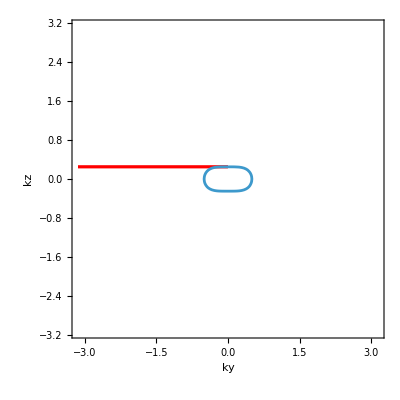

```mathematica
mu=0.25;lim=π;a1=0;Clear[κr];
c2=ContourPlot[(kz+a1^2 kz+4 a1 ky (((1+a1^2) ky)/(-1+a1^2)+√2 √((a1 (2 a1 ky^2+(-1+a1^2) kz))/((-1+a1^2)^2))))/(1-a1^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->Red, PlotLegends->Automatic,RegionFunction->Function[{ky,kz,z},((1+a1^2) ky)/(-1+a1^2)+√2 √((a1 (2 a1 ky^2+(-1+a1^2) kz))/((-1+a1^2)^2))>0 && a1 (2 a1 ky^2+(-1+a1^2) kz)>=0]]//Quiet;
c1=ContourPlot[(-4 a1 (1+a1^2) ky^2+kz-a1^4 kz+4 √2 a1 (-1+a1^2) ky √((a1 (2 a1 ky^2+(-1+a1^2) kz))/((-1+a1^2)^2)))/((-1+a1^2)^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->Red, PlotLegends->Automatic,RegionFunction->Function[{ky,kz,z},((1+a1^2) ky)/(-1+a1^2)-√2 √((a1 (2 a1 ky^2+(-1+a1^2) kz))/((-1+a1^2)^2))>0 && a1 (2 a1 ky^2+(-1+a1^2) kz)>=0]]//Quiet;

fs=ContourPlot[√((ky^2)^2+(kz)^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},Contours->20,PlotLegends->Automatic];
Show[c1,c2,fs]
Clear[κr,a1];
```

### sol 2

```mathematica
{en->-(4 (a1^2+b1^2) ky^2+a1 (-1+a1^2+b1^2) kz)/(a1 (1+a1^2+b1^2)),κrsq->ky^2+(b1^2 ky^2)/a1^2,ky κr->((-1+a1^2+b1^2) ky^2-a1 kz)/(1+a1^2+b1^2)}/.{a1->a Cos[t],b1->a Sin[t]}//FullSimplify
```

{en→(kz-a^2 kz-(4 a ky^2)/Cos[t])/(1+a^2),κrsq→ky^2/Cos[t]^2,ky κr→((-1+a^2) ky^2-a kz Cos[t])/(1+a^2)}

```mathematica
vals=FullSimplify[Solve[κr^2==ky^2/Cos[t]^2 && ky κr==((-1+a^2) ky^2-a kz Cos[t])/(1+a^2) && κr≠0, {a,κr} ],ass]
```

{{a→-(kz Cos[t]+√(kz^2 Cos[t]^2-4 ky^4 Tan[t]^2))/(2 ky^2 (-1+1/Cos[t])),κr→ky/Cos[t]},{a→(kz Cos[t]-√(kz^2 Cos[t]^2-4 ky^4 Tan[t]^2))/(2 ky^2 (1+1/Cos[t])),κr→-ky/Cos[t]},{a→(-kz Cos[t]+√(kz^2 Cos[t]^2-4 ky^4 Tan[t]^2))/(2 ky^2 (-1+1/Cos[t])),κr→ky/Cos[t]},{a→(kz Cos[t]+√(kz^2 Cos[t]^2-4 ky^4 Tan[t]^2))/(2 ky^2 (1+1/Cos[t])),κr→-ky/Cos[t]}}

```mathematica
FullSimplify[(kz-a^2 kz-(4 a ky^2)/Cos[t])/(1+a^2)/.vals,ass]
```

{-(√(kz^2 Cos[t]^2-4 ky^4 Tan[t]^2))/Cos[t],(√(kz^2 Cos[t]^2-4 ky^4 Tan[t]^2))/Cos[t],(√(kz^2 Cos[t]^2-4 ky^4 Tan[t]^2))/Cos[t],-(√(kz^2 Cos[t]^2-4 ky^4 Tan[t]^2))/Cos[t]}

```mathematica
Clear[t,μ];{ener,kap}={(√(kz^2 Cos[t]^2-4 ky^4 Tan[t]^2))/Cos[t](*(kz-a^2 kz-(4 a ky^2)/Cos[t])/(1+a^2)*),pm ky/Cos[t]};
soll=FullSimplify[Solve[kap==0 &&  ener==μ (*&& (ky^2)^2+(kz)^2==μ^2*),{ky,kz}],ass]
FullSimplify[ √((ky^2)^2+kz^2)/.soll,ass]
grad=FullSimplify[Grad[ener,{ky,kz}]/.soll,ass]
t=π/4;
tang1={grad[[1,2]],-grad[[1,1]]}
tang2={grad[[2,2]],-grad[[2,1]]}
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ky→0,kz→-μ},{ky→0,kz→μ}}

{μ,μ}

{{0,-(√(Cos[t]^2))/Cos[t]},{0,(√(Cos[t]^2))/Cos[t]}}

{-1,0}

{1,0}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ky→0,kz→-μ},{ky→0,kz→μ}}

{μ,μ}

{{0,(√(Cos[t]^2))/Cos[t]},{0,(√(Cos[t]^2))/Cos[t]}}

{1,0}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ky→0,kz→-μ},{ky→0,kz→μ}}

{μ,μ}

{{0,-(√(Cos[t]^2))/Cos[t]},{0,-(√(Cos[t]^2))/Cos[t]}}

{-1,0}

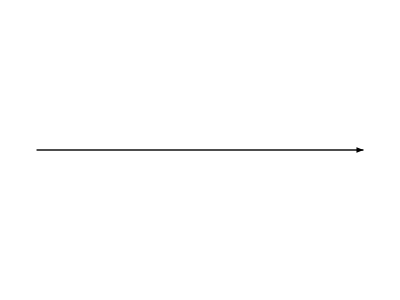
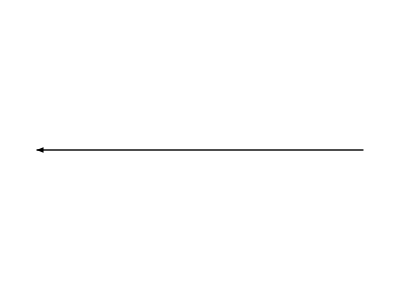

```mathematica
Clear[t,μ];{ener,kap}={kz(√(Cos[t]^2-4 ky^4 Tan[t]^2/kz^2))/Cos[t](*(kz-a^2 kz-(4 a ky^2)/Cos[t])/(1+a^2)*),pm ky/Cos[t]};
soll=FullSimplify[Solve[kap==0 &&  ener==μ (*&& (ky^2)^2+(kz)^2==μ^2*),{ky,kz}],ass]
FullSimplify[ √((ky^2)^2+kz^2)/.soll,ass]
grad=FullSimplify[Grad[ener,{ky,kz}]/.soll,ass]
t=π/4;
tang1={grad[[1,2]],-grad[[1,1]]}
(**********)
Clear[t,μ];{ener,kap}={-kz(√(Cos[t]^2-4 ky^4 Tan[t]^2/kz^2))/Cos[t](*(kz-a^2 kz-(4 a ky^2)/Cos[t])/(1+a^2)*),pm ky/Cos[t]};
soll=FullSimplify[Solve[kap==0 &&  ener==μ (*&& (ky^2)^2+(kz)^2==μ^2*),{ky,kz}],ass]
FullSimplify[ √((ky^2)^2+kz^2)/.soll,ass]
grad=FullSimplify[Grad[ener,{ky,kz}]/.soll,ass]
t=π/4;
tang2={grad[[1,2]],-grad[[1,1]]}
{Graphics[Arrow[{{0,0},tang1}]],Graphics[Arrow[{{0,0},tang2}]]}
Clear[t];
```

```mathematica
FullSimplify[Grad[kz(√(Cos[t]^2-4 ky^4 Tan[t]^2/kz^2))/Cos[t],{ky,kz}],ass]
%/.ky->0
FullSimplify[Grad[-kz(√(Cos[t]^2-4 ky^4 Tan[t]^2/kz^2))/Cos[t],{ky,kz}],ass]
%/.ky->0
FullSimplify[Grad[(√(kz^2 Cos[t]^2-4 ky^4 Tan[t]^2))/Cos[t],{ky,kz}],ass]
%/.ky->0
```

{-(8 ky^3 Tan[t]^2)/(kz Cos[t] √(Cos[t]^2-(4 ky^4 Tan[t]^2)/kz^2)),Cos[t]/(√(Cos[t]^2-(4 ky^4 Tan[t]^2)/kz^2))}

{0,Cos[t]/(√(Cos[t]^2))}

{(8 ky^3 Tan[t]^2)/(kz Cos[t] √(Cos[t]^2-(4 ky^4 Tan[t]^2)/kz^2)),-Cos[t]/(√(Cos[t]^2-(4 ky^4 Tan[t]^2)/kz^2))}

{0,-Cos[t]/(√(Cos[t]^2))}

{-(8 ky^3 Tan[t]^2)/(Cos[t] √(kz^2 Cos[t]^2-4 ky^4 Tan[t]^2)),(kz Cos[t])/(√(kz^2 Cos[t]^2-4 ky^4 Tan[t]^2))}

{0,(kz Cos[t])/(√(kz^2 Cos[t]^2))}

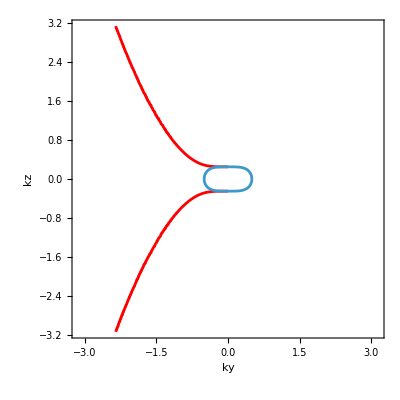

```mathematica
mu=0.25;lim=π;t=50;
c1=ContourPlot[kz(√(Cos[t]^2-4 ky^4 Tan[t]^2/kz^2))/Cos[t]==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->Red, PlotLegends->Automatic,RegionFunction->Function[{ky,kz,z},kz^2 Cos[t]^2-4 ky^4 Tan[t]^2>=0 && -ky/Cos[t]>0]]//Quiet;
c2=ContourPlot[-kz(√(Cos[t]^2-4 ky^4 Tan[t]^2/kz^2))/Cos[t]==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->Red, PlotLegends->Automatic,RegionFunction->Function[{ky,kz,z},kz^2 Cos[t]^2-4 ky^4 Tan[t]^2>=0 && -ky/Cos[t]>0]]//Quiet;

fs=ContourPlot[√((ky^2)^2+(kz)^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},Contours->20,PlotLegends->Automatic];
Show[c1,c2,fs]
Clear[t];
```

## Answer & Plot

```mathematica
ans={en->(√(kz^2 Cos[t]^2-4 ky^4 Tan[t]^2))/Cos[t],a1->a Cos[t],b1->a Sin[t], κr->sgn ky/Cos[t], a->sgn(kz Cos[t]-√(kz^2 Cos[t]^2-4 ky^4 Tan[t]^2))/(2 ky^2 (1+1/Cos[t]))}/.rep;
```

a\to \frac{\text{sgn} \left(k_z \cos (t)-\sqrt{k_z^2 \cos ^2(t)-4 k_y^4 \tan ^2(t)}\right)}{2 k_y^2 \left(\frac{1}{\cos (t)}+1\right)}

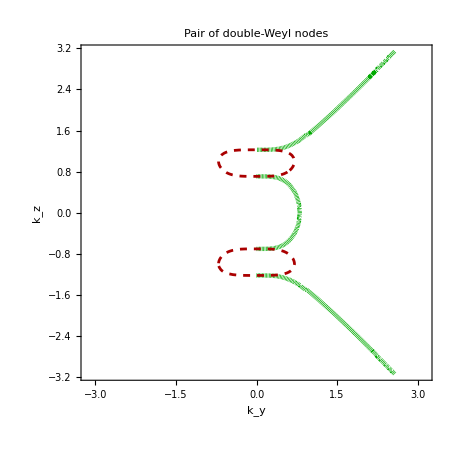

```mathematica
mu=0.5;lim=π;kw=1;th=0.007;t=π/6;
style={Directive[Darker[Cyan],Thickness[th],Opacity[0.75]],(**)Directive[Orange,Thickness[th],Opacity[0.75]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.0025]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.001]]};
c1=ContourPlot[(√((kz^2-kw^2)^2 Cos[t]^2-4 ky^4 Tan[t]^2))/Cos[t]==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style[[4]], RegionFunction->Function[{ky,kz,z},ky/Cos[t]>0]]//Quiet;
fs=ContourPlot[√((ky^2)^2+(kz^2-kw^2)^2)==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->{Directive[Darker[Red],Dashed]}];
plt=Show[c1,fs,Frame->True,Axes->False,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->450,PlotLabel->Style[(****)"Pair of double-Weyl nodes",20,FontFamily->"TexMaths Roman",Brown,Bold]]
SetDirectory[NotebookDirectory[]];
Export["doubleWeylarc.pdf",Rasterize[plt],ImageResolution->100];
Clear[t,kw];
```